```mathematica
μ=3.9877848 10^14;
Mp=1000;
l=50000;
a=6870000;

period = 2 π √(a^3/μ);
ranget =200*period;
animationrate = 500;(*dt per second*)



psiQ =τ ;

(*Position vectorc and linear kinetic energy (translation of centre of mass)*)
rm[t] = ({{rc[t] Cos[θ[t]]}, {rc[t] Sin[θ[t]]}, {0}});
rp1[t]=rm[t]+({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});
rp2[t]=rm[t]-({{l Cos[ψ[t]+θ[t]]}, {l  Sin[ψ[t]+θ[t]]}, {0}});

rm'[t]=D[rm[t], t];
rp1'[t]=D[rp1[t], t];
rp2'[t]=D[rp2[t], t];

Subscript[T, lin]=1/2 (2*Mp) (rc'[t]^2+rc[t]^2 θ'[t]^2);

(*Rotational kinetic energy (rotation of system about centre of mass)*)
ω[t]=({{0}, {0}, {(θ'[t]+ψ'[t])}});

Subscript[ⅈ, 123]=({{0, 0, 0}, {0, 2 Mp l^2, 0}, {0, 0, 2 Mp l^2}});

Subscript[T, rot]=1/2 Transpose[ω[t]].Subscript[ⅈ, 123].ω[t];

T=Subscript[T, lin]+Subscript[T, rot];

(*potential energy*)
Subscript[U, p1]=-(μ Mp)/(√(Transpose[rp1[t]].rp1[t]));
Subscript[U, p2]=-(μ Mp)/(√(Transpose[rp2[t]].rp2[t]));
V=Subscript[U, p1]+Subscript[U, p2];

L=T-V;
eqn1=Simplify[D[D[L, ψ'[t]], t]-D[L, ψ[t]]-psiQ];
eqn2 = Simplify[D[D[L, θ'[t]], t]-D[L, θ[t]]];
eqn3 = Simplify[D[D[L, rc'[t]], t]-D[L, rc[t]]];

func2[e_,τ_,alpha0_,psi0_,gamma0_]:=((*initial conditions and variable declaration *)



psidsh0 =0;

r0 = a (1-e);
rdsh0 = 0;

theta0 = 0;
thetadsh0=1/r0*√((μ (1+e))/(a (1-e)))  ;

system=NDSolve[{eqn1==0,eqn2==0,eqn3==0,
ψ[0]==psi0,ψ'[0]==psidsh0, θ[0] == theta0,θ'[0]==thetadsh0,rc[0] == r0,rc'[0]==0},
{ψ,α,θ,rc,γ},{t,0,ranget},
MaxSteps->∞,AccuracyGoal->Automatic,PrecisionGoal->10];

gammas[t_]:=Evaluate[γ[t]/.system[[1]]];
psis[t_]:=ψ[t]/.system[[1]];
alphas[t_]:=α[t]/.system[[1]];
thetas[t_]:=θ[t]/.system[[1]];
rs[t_]:=rc[t]/.system[[1]];
)
```

0.

0.0002

0.0004

0.0006

0.0008

0.001

0.0012

0.0014

0.0016

0.0018

0.002

0.0022

0.0024

0.0026

0.0028

0.003

0.0032

0.0034

0.0036

0.0038

0.004

0.0042

0.0044

0.0046

0.0048

0.005

0.0052

0.0054

0.0056

0.0058

0.006

0.0062

0.0064

0.0066

0.0068

0.007

0.0072

0.0074

0.0076

0.0078

0.008

0.0082

0.0084

0.0086

0.0088

0.009

0.0092

0.0094

0.0096

0.0098

0.01

0.0102

0.0104

0.0106

0.0108

0.011

0.0112

0.0114

0.0116

0.0118

0.012

0.0122

0.0124

0.0126

0.0128

0.013

0.0132

0.0134

0.0136

0.0138

0.014

0.0142

0.0144

0.0146

0.0148

0.015

0.0152

0.0154

0.0156

0.0158

0.016

0.0162

0.0164

0.0166

0.0168

0.017

0.0172

0.0174

0.0176

0.0178

0.018

0.0182

0.0184

0.0186

0.0188

0.019

0.0192

0.0194

0.0196

0.0198

0.02

0.0202

0.0204

0.0206

0.0208

0.021

0.0212

0.0214

0.0216

0.0218

0.022

0.0222

0.0224

0.0226

0.0228

0.023

0.0232

0.0234

0.0236

0.0238

0.024

0.0242

0.0244

0.0246

0.0248

0.025

0.0252

0.0254

0.0256

0.0258

0.026

0.0262

0.0264

0.0266

0.0268

0.027

0.0272

0.0274

0.0276

0.0278

0.028

0.0282

0.0284

0.0286

0.0288

0.029

0.0292

0.0294

0.0296

0.0298

0.03

0.0302

0.0304

0.0306

0.0308

0.031

0.0312

0.0314

0.0316

0.0318

0.032

0.0322

0.0324

0.0326

0.0328

0.033

0.0332

0.0334

0.0336

0.0338

0.034

0.0342

0.0344

0.0346

0.0348

0.035

0.0352

0.0354

0.0356

0.0358

0.036

0.0362

0.0364

0.0366

0.0368

0.037

0.0372

0.0374

0.0376

0.0378

0.038

0.0382

0.0384

0.0386

0.0388

0.039

0.0392

0.0394

0.0396

0.0398

0.04

0.0402

0.0404

0.0406

0.0408

0.041

0.0412

0.0414

0.0416

0.0418

0.042

0.0422

0.0424

0.0426

0.0428

0.043

0.0432

0.0434

0.0436

0.0438

0.044

0.0442

0.0444

0.0446

0.0448

0.045

0.0452

0.0454

0.0456

0.0458

0.046

0.0462

0.0464

0.0466

0.0468

0.047

0.0472

0.0474

0.0476

0.0478

0.048

0.0482

0.0484

0.0486

0.0488

0.049

0.0492

0.0494

0.0496

0.0498

0.05

0.0502

0.0504

0.0506

0.0508

0.051

0.0512

0.0514

0.0516

0.0518

0.052

0.0522

0.0524

0.0526

0.0528

0.053

0.0532

0.0534

0.0536

0.0538

0.054

0.0542

0.0544

0.0546

0.0548

0.055

0.0552

0.0554

0.0556

0.0558

0.056

0.0562

0.0564

0.0566

0.0568

0.057

0.0572

0.0574

0.0576

0.0578

0.058

0.0582

0.0584

0.0586

0.0588

0.059

0.0592

0.0594

0.0596

0.0598

0.06

0.0602

0.0604

0.0606

0.0608

0.061

0.0612

0.0614

0.0616

0.0618

0.062

0.0622

0.0624

0.0626

0.0628

0.063

0.0632

0.0634

0.0636

0.0638

0.064

0.0642

0.0644

0.0646

0.0648

0.065

0.0652

0.0654

0.0656

0.0658

0.066

0.0662

0.0664

0.0666

0.0668

0.067

0.0672

0.0674

0.0676

0.0678

0.068

0.0682

0.0684

0.0686

0.0688

0.069

0.0692

0.0694

0.0696

0.0698

0.07

0.0702

0.0704

0.0706

0.0708

0.071

0.0712

0.0714

0.0716

0.0718

0.072

0.0722

0.0724

0.0726

0.0728

0.073

0.0732

0.0734

0.0736

0.0738

0.074

0.0742

0.0744

0.0746

0.0748

0.075

0.0752

0.0754

0.0756

0.0758

0.076

0.0762

0.0764

0.0766

0.0768

0.077

0.0772

0.0774

0.0776

0.0778

0.078

0.0782

0.0784

0.0786

0.0788

0.079

0.0792

0.0794

0.0796

0.0798

0.08

0.0802

0.0804

0.0806

0.0808

0.081

0.0812

0.0814

0.0816

0.0818

0.082

0.0822

0.0824

0.0826

0.0828

0.083

0.0832

0.0834

0.0836

0.0838

0.084

0.0842

0.0844

0.0846

0.0848

0.085

0.0852

0.0854

0.0856

0.0858

0.086

0.0862

0.0864

0.0866

0.0868

0.087

0.0872

0.0874

0.0876

0.0878

0.088

0.0882

0.0884

0.0886

0.0888

0.089

0.0892

0.0894

0.0896

0.0898

0.09

0.0902

0.0904

0.0906

0.0908

0.091

0.0912

0.0914

0.0916

0.0918

0.092

0.0922

0.0924

0.0926

0.0928

0.093

0.0932

0.0934

0.0936

0.0938

0.094

0.0942

0.0944

0.0946

0.0948

0.095

0.0952

0.0954

0.0956

0.0958

0.096

0.0962

0.0964

0.0966

0.0968

0.097

0.0972

0.0974

0.0976

0.0978

0.098

0.0982

0.0984

0.0986

0.0988

0.099

0.0992

0.0994

0.0996

0.0998

0.1

0.1002

0.1004

0.1006

0.1008

0.101

0.1012

0.1014

0.1016

0.1018

0.102

0.1022

0.1024

0.1026

0.1028

0.103

0.1032

0.1034

0.1036

0.1038

0.104

0.1042

0.1044

0.1046

0.1048

0.105

0.1052

0.1054

0.1056

0.1058

0.106

0.1062

0.1064

0.1066

0.1068

0.107

0.1072

0.1074

0.1076

0.1078

0.108

0.1082

0.1084

0.1086

0.1088

0.109

0.1092

0.1094

0.1096

0.1098

0.11

0.1102

0.1104

0.1106

0.1108

0.111

0.1112

0.1114

0.1116

0.1118

0.112

0.1122

0.1124

0.1126

0.1128

0.113

0.1132

0.1134

0.1136

0.1138

0.114

0.1142

0.1144

0.1146

0.1148

0.115

0.1152

0.1154

0.1156

0.1158

0.116

0.1162

0.1164

0.1166

0.1168

0.117

0.1172

0.1174

0.1176

0.1178

0.118

0.1182

0.1184

0.1186

0.1188

0.119

0.1192

0.1194

0.1196

0.1198

0.12

0.1202

0.1204

0.1206

0.1208

0.121

0.1212

0.1214

0.1216

0.1218

0.122

0.1222

0.1224

0.1226

0.1228

0.123

0.1232

0.1234

0.1236

0.1238

0.124

0.1242

0.1244

0.1246

0.1248

0.125

0.1252

0.1254

0.1256

0.1258

0.126

0.1262

0.1264

0.1266

0.1268

0.127

0.1272

0.1274

0.1276

0.1278

0.128

0.1282

0.1284

0.1286

0.1288

0.129

0.1292

0.1294

0.1296

0.1298

0.13

0.1302

0.1304

0.1306

0.1308

0.131

0.1312

0.1314

0.1316

0.1318

0.132

0.1322

0.1324

0.1326

0.1328

0.133

0.1332

0.1334

0.1336

0.1338

0.134

0.1342

0.1344

0.1346

0.1348

0.135

0.1352

0.1354

0.1356

0.1358

0.136

0.1362

0.1364

0.1366

0.1368

0.137

0.1372

0.1374

0.1376

0.1378

0.138

0.1382

0.1384

0.1386

0.1388

0.139

0.1392

0.1394

0.1396

0.1398

0.14

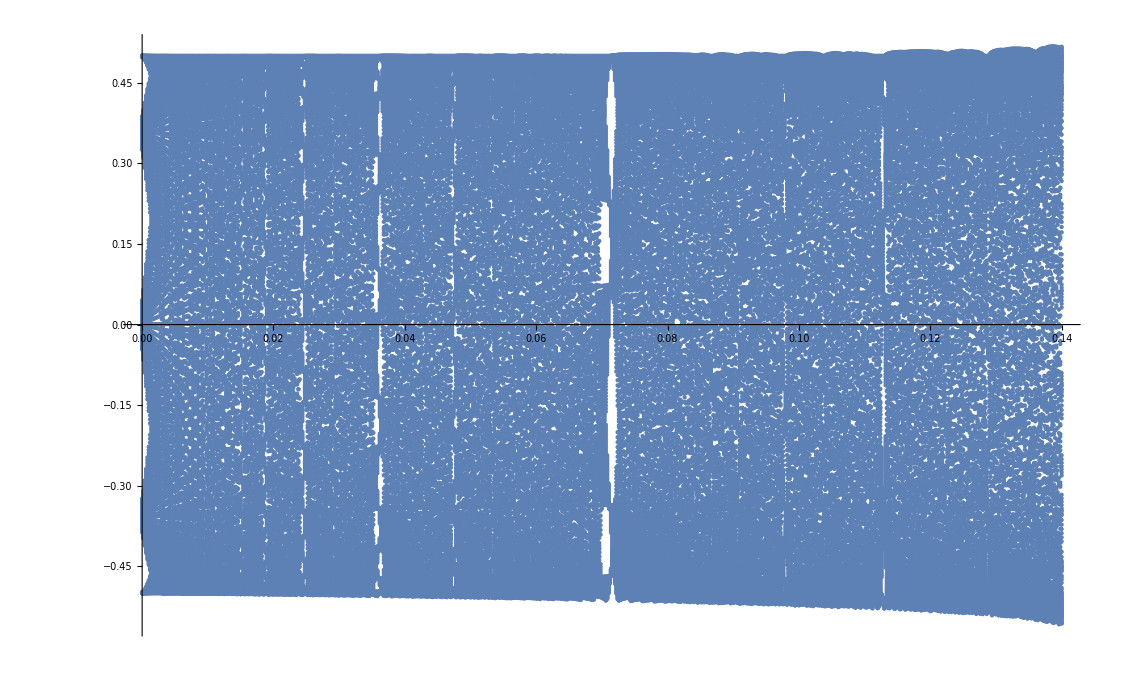

```mathematica
psistable = {};
Do[Print[e];func2[e,0,0,0.5,0];Do[psistable=Append[psistable,{e,psis[n*period]}],{n,0,200}],{e,0,0.14,0.0002}]
ListPlot[psistable]
```

```mathematica
Length[psistable]
psistable
```

140901

{{0.,0.5},{0.,-0.357442},{0.,0.000603722},{0.,0.35707},{0.,-0.499783},{0.,0.358161},{0.,-0.00101972},{0.,-0.356309},{0.,0.500003},{0.,-0.358416},{0.,0.00203507},{0.,0.356089},{0.,-0.499781},{0.,0.359151},{0.,-0.00247188},140872,{0.14,-0.351922},{0.14,0.26706},{0.14,-0.514952},{0.14,0.379445},{0.14,-0.554888},{0.14,0.434436},{0.14,-0.55581},{0.14,0.471322},{0.14,-0.52258},{0.14,0.47225},{0.14,-0.403359},{0.14,0.280384},{0.14,-0.132909},{0.14,-0.174398}}
 |  |  |  |

```mathematica
newtable = {};
Do[newtable=Append[newtable,{}],{200}]
Do[Do[newtable[[n]]=Append[newtable[[n]],psistable[[n+(j-1)*201]]],{j,1,700,1}],{n,1,200,1}]
```

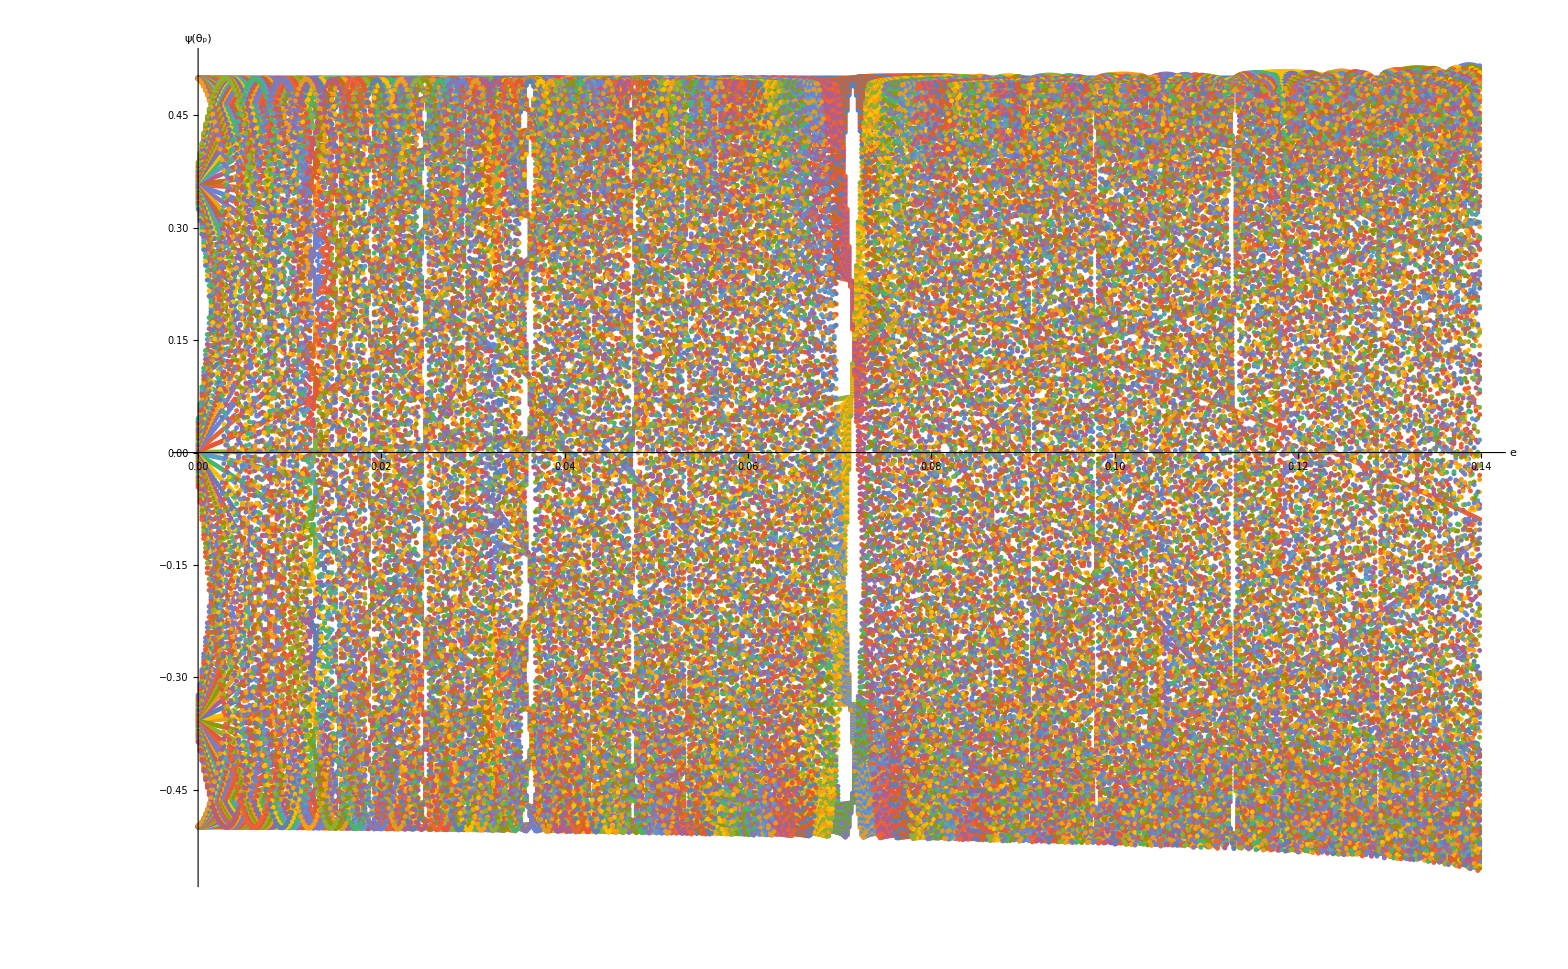

```mathematica
ListPlot[newtable,PlotMarkers->{•,5},AxesLabel->{Style["e",FontFamily->"Liberation Serif",25],Style["ψ(θ_p)",FontFamily->"Liberation Serif",25]},ImageSize->1680]
```